# Mathematica Overview

Lesson: Overviewhttps://vimeo.com/ondemand/mathematica/588030469Nonehttps://vimeo.com/ondemand/mathematica/588030469HyperlinkActionRecycledHyperlinkActive
Course: Mathematica Essentials

## Mathematics

### Numerical Calculations

```mathematica
1/2+5!-Sin[π/2]
```

239/2

```mathematica
Pi^E
```

π^ⅇ

```mathematica
N[Pi^E,30]
```

22.4591577183610454734271522045

### Algebra

```mathematica
Solve[3 x^2+5x-1==0,x]
```

{{x→1/6 (-5-√37)},{x→1/6 (-5+√37)}}

```mathematica
Solve[a x^2+b x+c==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
Solve[{2x+3y==1,5x-2y==6},{x,y}]
```

{{x→20/19,y→-7/19}}

### Calculus

```mathematica
f[x_]:=Sin[2x-1]*Cos[3x+2]
```

```mathematica
f[4]
```

Cos[14] Sin[7]

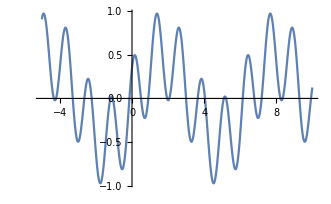

```mathematica
Plot[f[x],{x,-5,10}]
```

```mathematica
Integrate[f[x],x]
```

1/10 (5 Cos[3+x]-Cos[1+5 x])

```mathematica
Integrate[f[x],{x,0,5π}]
```

1/5 (Cos[1]-5 Cos[3])

```mathematica
∫_0^(5π) f[x]ⅆx
```

1/5 (Cos[1]-5 Cos[3])

## Science

### Chemistry

```mathematica
caffeine=Entity["Chemical","Caffeine"]
```

caffeine

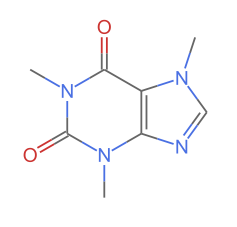

```mathematica
MoleculePlot[caffeine]
```

```mathematica
MoleculePlot3D[caffeine]
```

-Graphics3D-

### Astronomy

```mathematica
planets=EntityList["Planet"]
```

{Mercury,Venus,Earth,Mars,Jupiter,Saturn,Uranus,Neptune}

```mathematica
EntityProperties["Planet"]
```

{absolute magnitude H,age,albedo,alphanumeric name,alternate names,altitude,next maximum altitude,angular diameter,angular radius,largest distance from the Sun,largest distance from Sun,next apoapsis time,last apoapsis time,apparent altitude,apparent magnitude,longitude of ascending node Ω,atmospheric composition,atmospheric pressure,atmospheric scale height,authalic diameter,authalic radius,average distance from Earth,average orbit distance,average orbit velocity,average temperature,average heliocentric velocity,azimuth,above the horizon,classes,color,constellation,cylindrical equidistant texture,daily time above horizon,declination,mean density,average diameter,discoverers,discovery date,distance from Earth,distance from Sun,eccentric anomaly,orbital eccentricity,effective temperature,entity classes,equatorial angular velocity,equatorial circumference,equatorial diameter,equatorial frequency,equatorial radius,equatorial velocity,escape velocity,farthest planet,galactic latitude,galactic longitude,geocentric ecliptic latitude,geocentric ecliptic longitude,astrological symbol,gravitational constant mass product,gravity,Greenwich hour angle,heliocentric ecliptic latitude,heliocentric ecliptic longitude,heliocentric XYZ coordinates,heliocentric velocity vector,Hill radius,image,orbital inclination,local hour angle,orbital major axis,mass,next maximum altitude time,maximum temperature,mean anomaly,mean motion,minimum temperature,orbital minor axis,rotational moment of inertia,number of moons,NAIF identifier,name,nearest planet,north pole declination,north pole right ascension,object type,oblateness,obliquity,orbital angular momentum,orbital kinetic energy,orbital moment of inertia,orbit center,orbit circumference,orbit path,orbital period,orbit rules,smallest distance from Sun,argument of periapsis ω,longitude of periapsis ϖ,next periapsis time,last periapsis time,nearest distance from the Sun,polar circumference,polar diameter,polar radius,average radius,apparent direction,right ascension,ring system inner diameter,ring system inner radius,ring system outer diameter,ring system outer radius,ring system thickness,ring system width,next rise,Roche limit,rotational angular momentum,rotation period,known satellites,orbital semimajor axis,orbital semiminor axis,next set,shape,sidereal hour angle,solar day,solid angle,sphere of influence radius,stationary orbit radius,stationary orbit speed,surface area,3D graphic,true anomaly,instantaneous heliocentric velocity,volume,volumetric diameter,volumetric radius,zenith angle}

```mathematica
Entity["Planet","Jupiter"]["Satellites"]
```

{Metis,Adrastea,Amalthea,Thebe,Io,Europa,Ganymede,Callisto,Themisto,Leda,Ersa,Himalia,Pandia,Lysithea,Elara,Dia,S/2003 J12,Carpo,Valetudo,Euporie,Eupheme,S/2003 J18,S/2017 J7,S/2017 J3,S/2016 J1,Orthosie,Euanthe,Harpalyke,Praxidike,Thyone,S/2003 J16,S/2010 J1,S/2010 J2,Iocaste,Mneme,Hermippe,Thelxinoe,Helike,Ananke,S/2017 J9,S/2017 J6,Philophrosyne,Eurydome,S/2003 J24,Arche,Herse,Pasithee,S/2003 J10,Chaldene,S/2011 J2,Isonoe,S/2017 J5,S/2017 J8,Erinome,Kale,Aitne,S/2017 J2,Taygete,S/2003 J9,Carme,S/2011 J1,Sponde,Megaclite,Eirene,S/2003 J19,S/2017 J1,S/2003 J23,Kalyke,Kore,Pasiphae,Eukelade,S/2003 J4,Sinope,Hegemone,Aoede,Kallichore,Autonoe,Callirrhoe,Cyllene,S/2003 J2}

### Other Fields

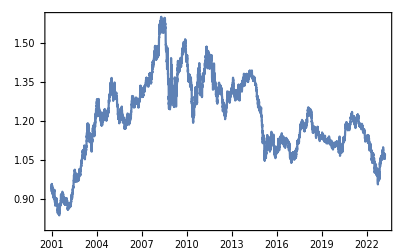

```mathematica
DateListPlot[FinancialData["EUR/USD",{2001,1,1}]]
```

```mathematica
GeoListPlot[{Entity["Country","NewZealand"]}]
```

-Graphics-

```mathematica
EntityProperties[Entity["Particle","CharmQuark"]]
```

{antiparticle,baryon number,bottomness,electric charge,electric charge,root mean square charge radius,charge states,charm,classical radius,Compton wavelength,charge conjugation,decay modes,decay type,electric charge density,entity classes,excitations,decay modes,full symbol,generic full symbol,generic symbol,spin g-factor,G-parity,half-life,hypercharge,isospin,isospin, G parity,isospin multiplet,isospin partners,isospin projection,lepton number,mean lifetime,mass,mass density,mean square charge radius,memberships,name,parity,interactions studied,PDG number,constituent quarks,quark model angular momentum state,quark content orbital angular momentum quantum number (L),quark content total spin quantum number (S),radioactivity,radius,spin,spin-parity,spin, parity, C parity,particle statistics,strangeness,symbol,topness,particle type,unobserved decay modes,width}

## Media

### Audio

```mathematica
?Audio*
```

```mathematica
song=Import["D:\\demo\\music.wav"]
```

Import::nffil: File D:\demo\music.wav not found during Import.

$Failed

```mathematica
AudioPlot[song]
```

AudioPlot::audio: Expecting an audio object instead of $Failed.

AudioPlot[$Failed]

```mathematica
AudioLength[song]
```

AudioLength::audio: Expecting an audio object instead of $Failed.

AudioLength[$Failed]

```mathematica
AudioSampleRate[song]
```

AudioSampleRate::audio: Expecting an audio object instead of $Failed.

AudioSampleRate[$Failed]

```mathematica
1440000/48000
```

30

### Images

```mathematica
?Image*
```

### Video

```mathematica
?Video*
```